```mathematica
Remove["Global`*"]
```

```mathematica
dataSD=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Phase Diagram\\Result_SD_Step=1000_T=0~2_B=0~4.csv"];
ListDensityPlot[dataSD,PlotLegends->Automatic]
```

```mathematica
Max[dataMz]
```

1244.94

```mathematica
dataMz=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Phase Diagram\\Result_Mz_Step=1000_T=0~2_B=0~4.csv"];
ListDensityPlot[dataMz,PlotLegends->Automatic]
```

-Graphics-

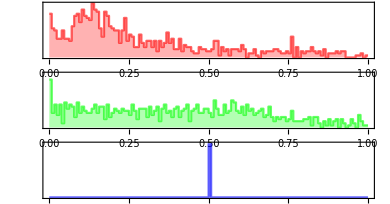

```mathematica
img=Image[Table[{(dataSD⟦i⟧⟦j⟧)/Max[dataSD],(dataMz⟦i⟧⟦j⟧)/Max[dataMz],0.5},{i,1,41},{j,1,21}],ColorSpace->"RGB",ImageSize->Small]
ImageHistogram[img,Appearance->"Separated",ImageSize->Medium]
```

```mathematica
img=ImageResize[%112,{500,500}]
```

```mathematica
ImageApply[# {0,0,0}&,img,Masking->EdgeDetect[img,100]]
```

```mathematica
Graphics[
Raster[ImageData@ImageReflect@img],
Frame->True,FrameTicks->{Table[{125i,i},{i,0,4,1}],Table[{250i,i},{i,0,2,0.5}]}
]
```

-Graphics-

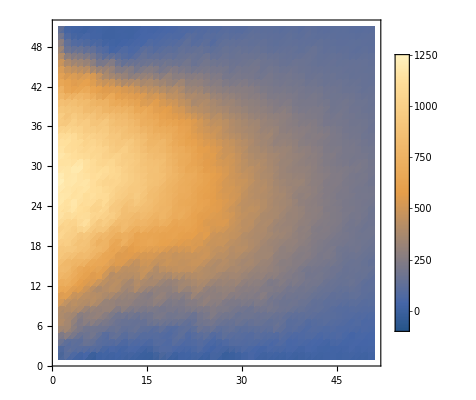

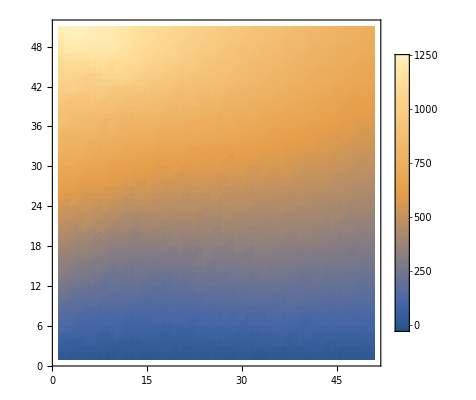

```mathematica
dataSD=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_SD_Step=1000_T=0~2_B=0~4.csv"];
ListDensityPlot[dataSD,PlotLegends->Automatic]
dataMz=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_Mz_Step=1000_T=0~2_B=0~4.csv"];
ListDensityPlot[dataMz,PlotLegends->Automatic]
```

```mathematica
img=ImageResize[%112,{500,500}]
```

-Graphics-

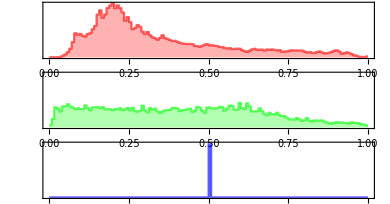

```mathematica
img=ImageResize[#,{500,500}]&@Image[Table[{(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@dataSD,(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@dataMz,0.5},{i,1,51},{j,1,51}],ColorSpace->"RGB",ImageSize->Small]
ImageHistogram[img,Appearance->"Separated",ImageSize->Medium]
```

```mathematica
Graphics[
Raster[ImageData@ImageReflect@img],
Frame->True,FrameTicks->{Table[{125i,i},{i,0,4,1}],Table[{250i,i},{i,0,2,0.5}]}
]
```

-Graphics-

```mathematica
EdgeDetect[Image[dataSD/1000,ColorSpace->"Grayscale"],15]
```

-Graphics-

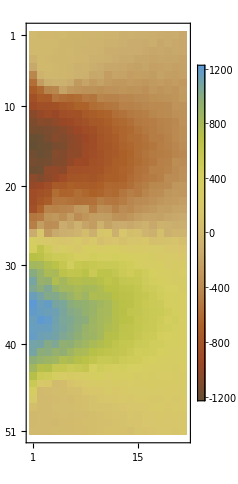

```mathematica
dataSD=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_SD_Step=1000_T=0~2_B=-5~5.csv"];
MatrixPlot[dataSD,PlotLegends->Automatic,PlotRange->All,ColorFunction->"SouthwestColors"]
```

```mathematica
dataSD=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_SD_Step=1000_T=0~2_B=-5~5.csv"];
ListDensityPlot[dataSD,PlotLegends->Automatic,ColorFunction->"SouthwestColors"]
dataMz=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_Mz_Step=1000_T=0~2_B=-5~5.csv"];
ListDensityPlot[dataMz,PlotLegends->Automatic,ColorFunction->"SouthwestColors"]
```

-Graphics-

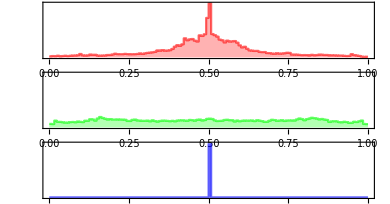

```mathematica
img=ImageResize[#,{200,200}]&@Image[Table[{(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@dataSD,(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@dataMz,0.5},{i,1,51},{j,1,21}],ColorSpace->"RGB",ImageSize->Small]
ImageHistogram[img,Appearance->"Separated",ImageSize->Medium]
```

```mathematica
36 36 100000 501
```

64929600000

```mathematica
36 36 10000 41 101
```

53667360000